```mathematica
ExplainContraction[g_,e_]:=Block[{
gBis=SortGraph[g], 
taken={e[[1]],e[[2]]},
comp=SortGraph[VertexDelete[VertexDelete[GraphComplement[g],e[[1]]],e[[2]]]],
result},
result=Table[
If[EdgeQ[gBis,e[[1]]<->v],
If[EdgeQ[gBis,e[[2]]<->v],
{"DoubleEdgeDisappears",e[[1]]<->v},
{"ShadowDisappears"<>ToString[e[[2]]],e[[2]]<->v}
],
If[EdgeQ[gBis,e[[2]]<->v],
{"ShadowDisappears"<>ToString[e[[1]]],e[[1]]<->v},
{Style["DoubleNonEdgeDisappears",Red],e[[2]]<->v}
]
]
,{v,Select[VertexList[gBis],!MemberQ[taken,#]&]}
];
Join[result,
Map[{Style["Unchanged",Darker[Green]],#}&,EdgeList[comp]]
]
]
```

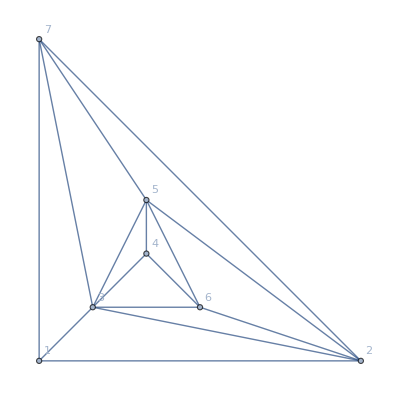

```mathematica
Graph[ReadGrof[5],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```

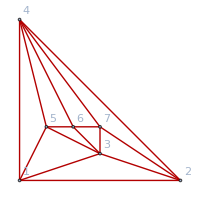
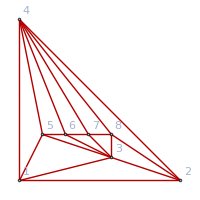
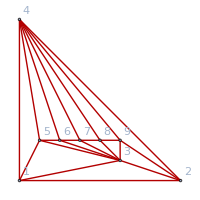
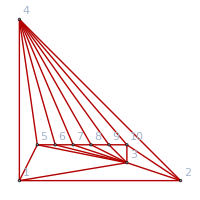
{-Graphics-
{2<->4<->{DoubleEdgeDisappears,2<->1}
{DoubleEdgeDisappears,2<->7}
{ShadowDisappears2,2<->5}
{ShadowDisappears2,2<->6}
{ShadowDisappears4,4<->3}
{Unchanged,1<->6}
{Unchanged,1<->7}
{Unchanged,5<->7},3<->2<->{DoubleEdgeDisappears,3<->1}
{DoubleEdgeDisappears,3<->7}
{ShadowDisappears2,2<->5}
{ShadowDisappears2,2<->6}
{ShadowDisappears3,3<->4}
{Unchanged,1<->6}
{Unchanged,1<->7}
{Unchanged,5<->7},6<->3<->{DoubleEdgeDisappears,6<->5}
{DoubleEdgeDisappears,6<->7}
{ShadowDisappears3,3<->4}
{ShadowDisappears6,6<->1}
{ShadowDisappears6,6<->2}
{Unchanged,1<->7}
{Unchanged,2<->5}
{Unchanged,5<->7}},-Graphics-
{5<->4<->{DoubleEdgeDisappears,5<->1}
{DoubleEdgeDisappears,5<->6}
{ShadowDisappears4,4<->3}
{ShadowDisappears5,5<->2}
{ShadowDisappears5,5<->7}
{ShadowDisappears5,5<->8}
{Unchanged,1<->6}
{Unchanged,1<->7}
{Unchanged,1<->8}
{Unchanged,2<->6}
{Unchanged,2<->7}
{Unchanged,6<->8},8<->4<->{DoubleEdgeDisappears,8<->2}
{DoubleEdgeDisappears,8<->7}
{ShadowDisappears4,4<->3}
{ShadowDisappears8,8<->1}
{ShadowDisappears8,8<->5}
{ShadowDisappears8,8<->6}
{Unchanged,1<->6}
{Unchanged,1<->7}
{Unchanged,2<->5}
{Unchanged,2<->6}
{Unchanged,2<->7}
{Unchanged,5<->7},8<->7<->{DoubleEdgeDisappears,8<->3}
{DoubleEdgeDisappears,8<->4}
{ShadowDisappears7,7<->2}
{ShadowDisappears8,8<->6}
{DoubleNonEdgeDisappears,7<->1}
{DoubleNonEdgeDisappears,7<->5}
{Unchanged,1<->6}
{Unchanged,2<->5}
{Unchanged,2<->6}
{Unchanged,3<->4}},-Graphics-
{2<->4<->{DoubleEdgeDisappears,2<->1}
{DoubleEdgeDisappears,2<->9}
{ShadowDisappears2,2<->5}
{ShadowDisappears2,2<->6}
{ShadowDisappears2,2<->7}
{ShadowDisappears2,2<->8}
{ShadowDisappears4,4<->3}
{Unchanged,1<->6}
{Unchanged,1<->7}
{Unchanged,1<->8}
{Unchanged,1<->9}
{Unchanged,5<->7}
{Unchanged,5<->8}
{Unchanged,5<->9}
{Unchanged,6<->8}
{Unchanged,6<->9}
{Unchanged,7<->9},3<->1<->{DoubleEdgeDisappears,3<->2}
{DoubleEdgeDisappears,3<->5}
{ShadowDisappears1,1<->6}
{ShadowDisappears1,1<->7}
{ShadowDisappears1,1<->8}
{ShadowDisappears1,1<->9}
{ShadowDisappears3,3<->4}
{Unchanged,2<->5}
{Unchanged,2<->6}
{Unchanged,2<->7}
{Unchanged,2<->8}
{Unchanged,5<->7}
{Unchanged,5<->8}
{Unchanged,5<->9}
{Unchanged,6<->8}
{Unchanged,6<->9}
{Unchanged,7<->9},6<->5<->{DoubleEdgeDisappears,6<->3}
{DoubleEdgeDisappears,6<->4}
{ShadowDisappears5,5<->7}
{ShadowDisappears6,6<->1}
{DoubleNonEdgeDisappears,5<->2}
{DoubleNonEdgeDisappears,5<->8}
{DoubleNonEdgeDisappears,5<->9}
{Unchanged,1<->7}
{Unchanged,1<->8}
{Unchanged,1<->9}
{Unchanged,2<->7}
{Unchanged,2<->8}
{Unchanged,3<->4}
{Unchanged,7<->9}},-Graphics-
{6<->3<->{DoubleEdgeDisappears,6<->5}
{DoubleEdgeDisappears,6<->7}
{ShadowDisappears3,3<->4}
{ShadowDisappears6,6<->1}
{ShadowDisappears6,6<->2}
{ShadowDisappears6,6<->8}
{ShadowDisappears6,6<->9}
{ShadowDisappears6,6<->10}
{Unchanged,1<->7}
{Unchanged,1<->8}
{Unchanged,1<->9}
{Unchanged,1<->10}
{Unchanged,2<->5}
{Unchanged,2<->7}
{Unchanged,2<->8}
{Unchanged,2<->9}
{Unchanged,5<->7}
{Unchanged,5<->8}
{Unchanged,5<->9}
{Unchanged,5<->10}
{Unchanged,7<->9}
{Unchanged,7<->10}
{Unchanged,8<->10},10<->2<->{DoubleEdgeDisappears,10<->3}
{DoubleEdgeDisappears,10<->4}
{ShadowDisappears10,10<->1}
{ShadowDisappears2,2<->9}
{DoubleNonEdgeDisappears,2<->5}
{DoubleNonEdgeDisappears,2<->6}
{DoubleNonEdgeDisappears,2<->7}
{DoubleNonEdgeDisappears,2<->8}
{Unchanged,1<->6}
{Unchanged,1<->7}
{Unchanged,1<->8}
{Unchanged,1<->9}
{Unchanged,3<->4}
{Unchanged,5<->7}
{Unchanged,5<->8}
{Unchanged,5<->9}
{Unchanged,6<->8}
{Unchanged,6<->9}
{Unchanged,7<->9},10<->9<->{DoubleEdgeDisappears,10<->3}
{DoubleEdgeDisappears,10<->4}
{ShadowDisappears10,10<->8}
{ShadowDisappears9,9<->2}
{DoubleNonEdgeDisappears,9<->1}
{DoubleNonEdgeDisappears,9<->5}
{DoubleNonEdgeDisappears,9<->6}
{DoubleNonEdgeDisappears,9<->7}
{Unchanged,1<->6}
{Unchanged,1<->7}
{Unchanged,1<->8}
{Unchanged,2<->5}
{Unchanged,2<->6}
{Unchanged,2<->7}
{Unchanged,2<->8}
{Unchanged,3<->4}
{Unchanged,5<->7}
{Unchanged,5<->8}
{Unchanged,6<->8}}}

```mathematica
Table[
With[{g=JacobsThalGraph[k]},
Column[{Graph[g,VertexLabels->"Name", GraphLayout->"PlanarEmbedding",GraphHighlight->CollectMPGEdges[g],GraphHighlightStyle->"Thick", ImageSize->200],
Sort[Table[
e<->Column[Sort[ExplainContraction[g,e]]],{e,RandomSample[CollectMPGEdges[g],3]}
]]}]]
,{k,3,6}]
```

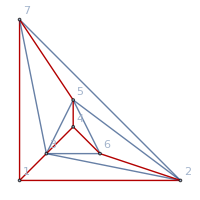
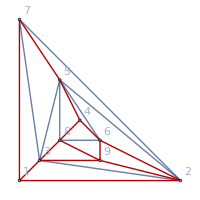
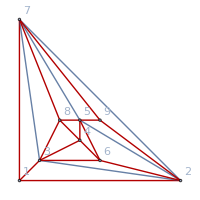
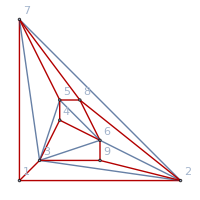
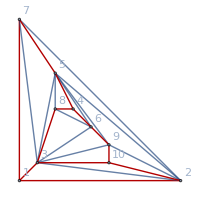
{-Graphics-
{3<->4<->{DoubleEdgeDisappears,3<->5}
{DoubleEdgeDisappears,3<->6}
{ShadowDisappears4,4<->1}
{ShadowDisappears4,4<->2}
{ShadowDisappears4,4<->7}
{Unchanged,1<->5}
{Unchanged,1<->6}
{Unchanged,6<->7},4<->5<->{DoubleEdgeDisappears,4<->3}
{DoubleEdgeDisappears,4<->6}
{ShadowDisappears4,4<->2}
{ShadowDisappears4,4<->7}
{DoubleNonEdgeDisappears,5<->1}
{Unchanged,1<->6}
{Unchanged,6<->7},4<->6<->{DoubleEdgeDisappears,4<->3}
{DoubleEdgeDisappears,4<->5}
{ShadowDisappears4,4<->2}
{DoubleNonEdgeDisappears,6<->1}
{DoubleNonEdgeDisappears,6<->7}
{Unchanged,1<->5}},-Graphics-
{3<->8<->{DoubleEdgeDisappears,3<->5}
{DoubleEdgeDisappears,3<->9}
{ShadowDisappears3,3<->4}
{ShadowDisappears3,3<->6}
{ShadowDisappears8,8<->1}
{ShadowDisappears8,8<->2}
{ShadowDisappears8,8<->7}
{Unchanged,1<->4}
{Unchanged,1<->5}
{Unchanged,1<->6}
{Unchanged,1<->9}
{Unchanged,2<->4}
{Unchanged,4<->7}
{Unchanged,4<->9}
{Unchanged,5<->9}
{Unchanged,6<->7}
{Unchanged,7<->9},4<->5<->{DoubleEdgeDisappears,4<->6}
{DoubleEdgeDisappears,4<->8}
{ShadowDisappears4,4<->2}
{ShadowDisappears4,4<->3}
{ShadowDisappears4,4<->7}
{DoubleNonEdgeDisappears,5<->1}
{DoubleNonEdgeDisappears,5<->9}
{Unchanged,1<->6}
{Unchanged,1<->8}
{Unchanged,1<->9}
{Unchanged,2<->8}
{Unchanged,3<->6}
{Unchanged,6<->7}
{Unchanged,7<->8}
{Unchanged,7<->9},4<->8<->{DoubleEdgeDisappears,4<->5}
{DoubleEdgeDisappears,4<->6}
{ShadowDisappears4,4<->3}
{ShadowDisappears4,4<->9}
{DoubleNonEdgeDisappears,8<->1}
{DoubleNonEdgeDisappears,8<->2}
{DoubleNonEdgeDisappears,8<->7}
{Unchanged,1<->5}
{Unchanged,1<->6}
{Unchanged,1<->9}
{Unchanged,3<->6}
{Unchanged,5<->9}
{Unchanged,6<->7}
{Unchanged,7<->9}},-Graphics-
{2<->6<->{DoubleEdgeDisappears,2<->3}
{DoubleEdgeDisappears,2<->5}
{ShadowDisappears2,2<->4}
{ShadowDisappears6,6<->1}
{ShadowDisappears6,6<->7}
{ShadowDisappears6,6<->9}
{DoubleNonEdgeDisappears,6<->8}
{Unchanged,1<->4}
{Unchanged,1<->5}
{Unchanged,1<->8}
{Unchanged,1<->9}
{Unchanged,3<->5}
{Unchanged,3<->9}
{Unchanged,4<->7}
{Unchanged,4<->9}
{Unchanged,8<->9},3<->8<->{DoubleEdgeDisappears,3<->4}
{DoubleEdgeDisappears,3<->7}
{ShadowDisappears3,3<->5}
{ShadowDisappears8,8<->1}
{ShadowDisappears8,8<->2}
{ShadowDisappears8,8<->6}
{DoubleNonEdgeDisappears,8<->9}
{Unchanged,1<->4}
{Unchanged,1<->5}
{Unchanged,1<->6}
{Unchanged,1<->9}
{Unchanged,2<->4}
{Unchanged,4<->7}
{Unchanged,4<->9}
{Unchanged,6<->7}
{Unchanged,6<->9},4<->5<->{DoubleEdgeDisappears,4<->6}
{DoubleEdgeDisappears,4<->8}
{ShadowDisappears4,4<->2}
{ShadowDisappears4,4<->7}
{ShadowDisappears4,4<->9}
{ShadowDisappears5,5<->3}
{DoubleNonEdgeDisappears,5<->1}
{Unchanged,1<->6}
{Unchanged,1<->8}
{Unchanged,1<->9}
{Unchanged,2<->8}
{Unchanged,3<->9}
{Unchanged,6<->7}
{Unchanged,6<->8}
{Unchanged,6<->9}
{Unchanged,8<->9}},-Graphics-
{2<->8<->{DoubleEdgeDisappears,2<->6}
{DoubleEdgeDisappears,2<->7}
{ShadowDisappears2,2<->5}
{ShadowDisappears8,8<->1}
{ShadowDisappears8,8<->3}
{ShadowDisappears8,8<->9}
{DoubleNonEdgeDisappears,8<->4}
{Unchanged,1<->4}
{Unchanged,1<->5}
{Unchanged,1<->6}
{Unchanged,1<->9}
{Unchanged,4<->7}
{Unchanged,4<->9}
{Unchanged,5<->9}
{Unchanged,6<->7}
{Unchanged,7<->9},5<->8<->{DoubleEdgeDisappears,5<->6}
{DoubleEdgeDisappears,5<->7}
{ShadowDisappears5,5<->2}
{ShadowDisappears8,8<->3}
{ShadowDisappears8,8<->4}
{DoubleNonEdgeDisappears,8<->1}
{DoubleNonEdgeDisappears,8<->9}
{Unchanged,1<->4}
{Unchanged,1<->6}
{Unchanged,1<->9}
{Unchanged,2<->4}
{Unchanged,4<->7}
{Unchanged,4<->9}
{Unchanged,6<->7}
{Unchanged,7<->9},7<->8<->{DoubleEdgeDisappears,7<->2}
{DoubleEdgeDisappears,7<->5}
{ShadowDisappears7,7<->6}
{ShadowDisappears8,8<->1}
{ShadowDisappears8,8<->3}
{DoubleNonEdgeDisappears,8<->4}
{DoubleNonEdgeDisappears,8<->9}
{Unchanged,1<->4}
{Unchanged,1<->5}
{Unchanged,1<->6}
{Unchanged,1<->9}
{Unchanged,2<->4}
{Unchanged,2<->5}
{Unchanged,4<->9}
{Unchanged,5<->9}},-Graphics-
{2<->10<->{DoubleEdgeDisappears,2<->3}
{DoubleEdgeDisappears,2<->9}
{ShadowDisappears10,10<->1}
{ShadowDisappears10,10<->5}
{ShadowDisappears10,10<->7}
{DoubleNonEdgeDisappears,10<->4}
{DoubleNonEdgeDisappears,10<->6}
{DoubleNonEdgeDisappears,10<->8}
{Unchanged,1<->4}
{Unchanged,1<->5}
{Unchanged,1<->6}
{Unchanged,1<->8}
{Unchanged,1<->9}
{Unchanged,3<->4}
{Unchanged,4<->7}
{Unchanged,4<->9}
{Unchanged,6<->7}
{Unchanged,7<->8}
{Unchanged,7<->9}
{Unchanged,8<->9},4<->5<->{DoubleEdgeDisappears,4<->6}
{DoubleEdgeDisappears,4<->8}
{ShadowDisappears4,4<->2}
{ShadowDisappears4,4<->3}
{ShadowDisappears4,4<->7}
{ShadowDisappears4,4<->9}
{DoubleNonEdgeDisappears,5<->1}
{DoubleNonEdgeDisappears,5<->10}
{Unchanged,1<->6}
{Unchanged,1<->8}
{Unchanged,1<->9}
{Unchanged,1<->10}
{Unchanged,2<->6}
{Unchanged,2<->8}
{Unchanged,6<->7}
{Unchanged,6<->10}
{Unchanged,7<->8}
{Unchanged,7<->9}
{Unchanged,7<->10}
{Unchanged,8<->9}
{Unchanged,8<->10},4<->8<->{DoubleEdgeDisappears,4<->5}
{DoubleEdgeDisappears,4<->6}
{ShadowDisappears4,4<->3}
{DoubleNonEdgeDisappears,8<->1}
{DoubleNonEdgeDisappears,8<->2}
{DoubleNonEdgeDisappears,8<->7}
{DoubleNonEdgeDisappears,8<->9}
{DoubleNonEdgeDisappears,8<->10}
{Unchanged,1<->5}
{Unchanged,1<->6}
{Unchanged,1<->9}
{Unchanged,1<->10}
{Unchanged,2<->6}
{Unchanged,5<->10}
{Unchanged,6<->7}
{Unchanged,6<->10}
{Unchanged,7<->9}
{Unchanged,7<->10}}}

```mathematica
Table[
With[{g=ReadGrof[k]},
Column[{Graph[g,VertexLabels->"Name", GraphLayout->"PlanarEmbedding",GraphHighlight->CollectMPGEdges[g],GraphHighlightStyle->"Thick", ImageSize->200],
Sort[Table[
e<->Column[Sort[ExplainContraction[g,e]]],{e,RandomSample[CollectMPGEdges[g],3]}
]]}]]
,{k,5,100,20}]
```